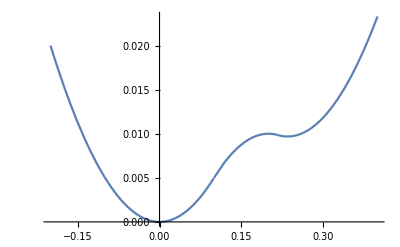

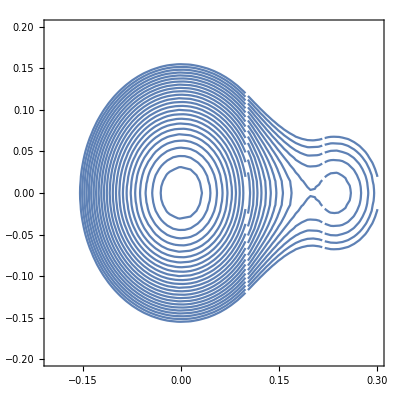

```mathematica
c=0.2;
a=0.235;
d=c^2/4;
b=(2 a c -a^2)/4;
x1=c/2;
x2=(c+a)/2;
V1[x_]:=Piecewise[{{1/2 x^2,x<x1},{-1/2(x-c)^2+d,x1<x<x2},{1/2(x-a)^2+b,x>x2}},x]
Plot[V1[x],{x,-.2,.4}]
Table[ContourPlot[y^2/2+V1[x]== En,{x,-0.2,0.3},{y,-0.2,0.2}],{En,0,0.012,0.0005}];
Show[%]
```

0.000625

1

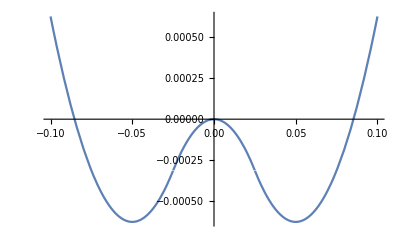

```mathematica
a2=0.05;
y1 = -a2/2;
y2 = a2/2;
b2=y1^2+y1 a2+ 1/2 a2^2
s=1
V2[y_]:=s(Piecewise[{{1/2(y+a2)^2,y<y1},{-1/2 y^2+b2,y1<y<y2},{1/2(y-a2)^2,y>y2}},y]-b2)
Plot[V2[y],{y,-.1,.1}]
```

```mathematica
α = 0.2;
χ = a2;
x3 =α/2
x4=χ/2;
δ=-x4^2+β+x4 χ-1/2 χ^2;
β = x3^2-x3 α+ 1/2 α^2
H[x_,y_]:= Piecewise[{{1/2 y^2+ 1/2(x+α)^2,x≤ -x3},{1/2 y^2 -1/2 x^2+β,-x3<x≤ 0},{V2[y] x/x4+1/2 y^2(1-x/x4)-1/2 x^2+β,0<x≤ x4},{  V2[y]+1/2(x-χ)^2+δ,x>x4}},x]
```

0.1

0.01

```mathematica
Manipulate[Plot[H[a,b],{a,-0.3,0.2}],{b,-2,2}]
```

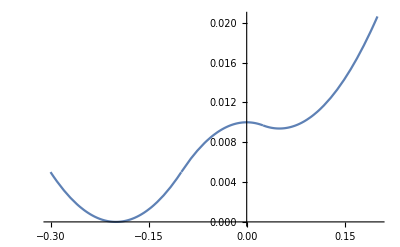

```mathematica
Plot[H[a,0],{a,-0.3,0.2}]
```

```mathematica
Plot3D[H[x,y],{x,-0.4,0.15},{y,- 0.2,0.2}]
```

-Graphics3D-

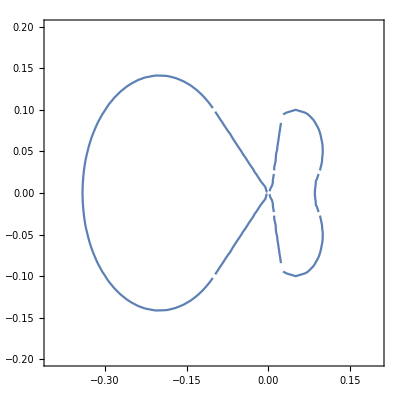

```mathematica
ContourPlot[H[x,y]== 0.01,{x,-0.4,0.2},{y,- 0.2,0.2}]
```

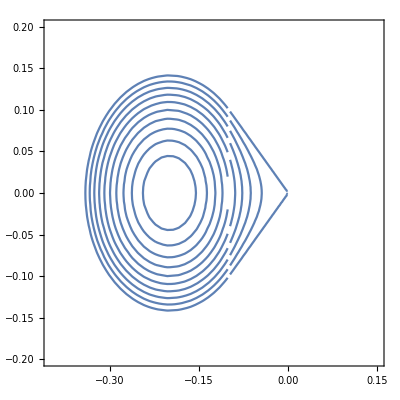

```mathematica
Table[ContourPlot[H[x,y]== En,{x,-0.4,0.15},{y,- 0.2,0.2}],{En,0,0.01,0.001}];
Show[%]
```

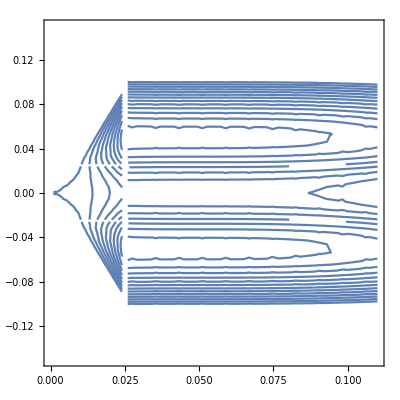

```mathematica
Table[ContourPlot[H[x,y]== En,{x,0,0.11},{y,- 0.15,0.15}],{En,0,0.01,0.0001}];
Show[%]
```

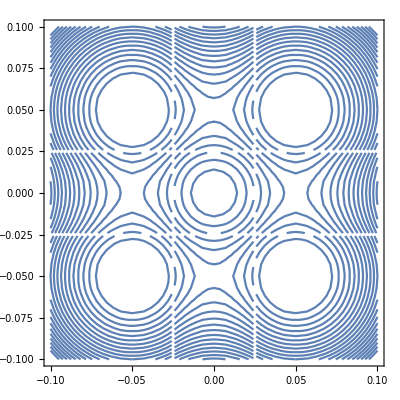

```mathematica
Table[ContourPlot[V2[x]+V2[y]== En,{x,-0.1,0.1},{y,- 0.1,0.1}],{En,-0.001,0.001,0.0001}];
Show[%]
```

```mathematica
f[x_,y_]:=y^4+x^4+x^3+2 x^2 y^2- 2 y^2 x
```

```mathematica
Manipulate[ContourPlot[a y^4+b x^4+c x^3+d x^2 y^2+ e y^2 x +f x^3 y + g x y^3 == 0,{x,-4,4},{y,- 4,4}],{a,-5,5},{b,-5,5},{c,-5,5},{d,-5,5},{e,-5,5},{f,-5,5},{g,-5,5}]
```

```mathematica
f[x_,y_]:=y^4+x^4+4 x^3+2 x^2 y^2- 4 y^2 x
```

```mathematica
Normal[Series[f[x,y],{x,0,3},{y,0,3}]]
D[%,x]
```

4 x^3-4 x y^2+2 x^2 y^2

12 x^2-4 y^2+4 x y^2

```mathematica
Clear[a]
```

```mathematica
-D[f[x,y],x]
Normal[Series[%,{x,0,2},{y,0,2}]]
```

-12 x^2-4 x^3+4 y^2-4 x y^2

-12 x^2+4 y^2-4 x y^2

```mathematica
a[x_,y_]:=-12 x^2+4 y^2-4 x y^2
```

```mathematica
D[f[x,y],y]
Normal[Series[%,{x,0,2},{y,0,2}]]
```

-8 x y+4 x^2 y+4 y^3

-8 x y+4 x^2 y

```mathematica
b[x_,y_]:=-8 x y+4 x^2 y
```

```mathematica
Manipulate[Module[{sol=NDSolve[{x'[t]==b[x[t],y[t]],y'[t]==a[x[t],y[t]],y[0]== p[[2]],x[0]==p[[1]]},{x[t],y[t]},{t,0,T}]},ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,T},PlotRange->{{-4,2},{-2,2}}]],{{p,{2,1}},Locator},{{T,10},0,100}]
```

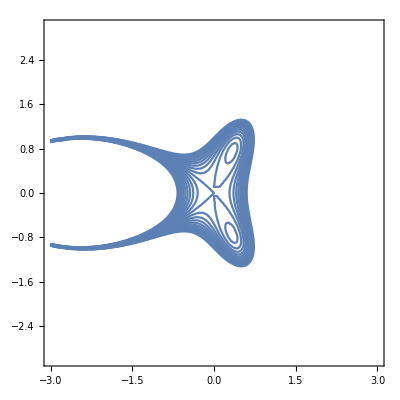

```mathematica
Table[ContourPlot[f[x,y]== En,{x,-3,3},{y,- 3,3}],{En,-1,1,.1}];
Show[%]
```

```mathematica
a=2;
Plot3D[f[x,y],{x,-a,a},{y,-a,a}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[f[b,a],{a,-1,1},PlotRange-> {{-1,1},{-0.75,0.75}}],{b,-1,1}]
```

```mathematica
Normal[Series[f[x,y],{x,0,3},{y,0,3}]]
```

4 x^3-4 x y^2+2 x^2 y^2

```mathematica
Table[ContourPlot[Normal[Series[f[x,y],{x,0,3},{y,0,3}]]== En,{x,-3,3},{y,- 3,3}],{En,-1,1,.1}];
Show[%]
```

-Graphics-

```mathematica
f[x,y]
```

4 x^3+x^4-4 x y^2+2 x^2 y^2+y^4

```mathematica
FindMinimum[f[x,y],{{x,0.4},{y,0.6}}]
```

{-0.148148,{x→0.333333,y→0.745356}}

```mathematica
sol =DSolve[{y'[t]== 
4 x[t]^3+4 y[t]^2 x[t]-6x[t]y[t],x'[t]== -4 y[t]^3-3 y[t]^2-4y[t] x[t]^2+3 x[t]^2},{y[t],x[t]},t]
```

DSolve[{y'[t]==4 x[t]^3-6 x[t] y[t]+4 x[t] y[t]^2,x'[t]==3 x[t]^2-4 x[t]^2 y[t]-3 y[t]^2-4 y[t]^3},{y[t],x[t]},t]

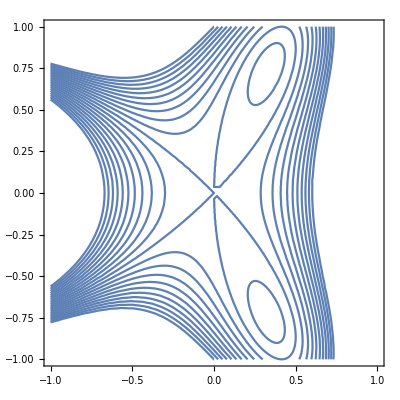

```mathematica
Table[ContourPlot[f[x,y]== En,{x,-1,1},{y,- 1,1}],{En,-1,1,.1}];
Show[%]
```

```mathematica
D[f[x,y],y]
```

-8 x y+4 x^2 y+4 y^3

```mathematica
D[f[x,y],x]//Factor
```

4 (3 x^2+x^3-y^2+x y^2)

```mathematica
Manipulate[Module[{sol=NDSolve[{x'[t]== D[f[x[t],y[t]],y[t]],y'[t]==-D[f[x[t],y[t]],x[t]],y[0]== p[[2]],x[0]==p[[1]]},{x[t],y[t]},{t,0,T}]},ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,T},PlotRange->{{-4,2},{-2,2}}]],{{p,{2,1}},Locator},{{T,10},0,100}]
```

```mathematica
f[x,y]
D[f[x,y],x]
```

4 x^3+x^4-4 x y^2+2 x^2 y^2+y^4

12 x^2+4 x^3-4 y^2+4 x y^2

```mathematica
y1[x0_,y0_]:= y0 - D[f[x0,y0],x0]
x1[x0_,y0_] := x0  + D[f[x0,y1[x0,y0]],y0]
```

0.334276

0.0504133

1

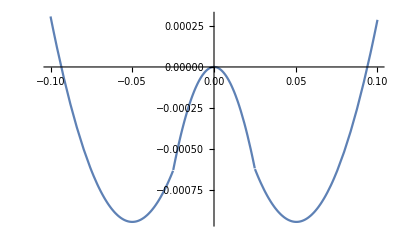

```mathematica
a2=0.05;
y1 = -a2/2;
y2 = a2/2;
b2=-1/3(y1-1)^3+y1+1/2(y1+a2)^2
a3=y2+√(2(1/3(y2-1)^3-y2+b2))
s=1
V2[y_]:=s(Piecewise[{{1/2(y+a2)^2,y<y1},{1/3(y-1)^3+-y +b2,y1<y<y2},{1/2(y-a3)^2,y>y2}},y]-b2+1/3)
Plot[V2[y],{y,-.1,.1}]
```

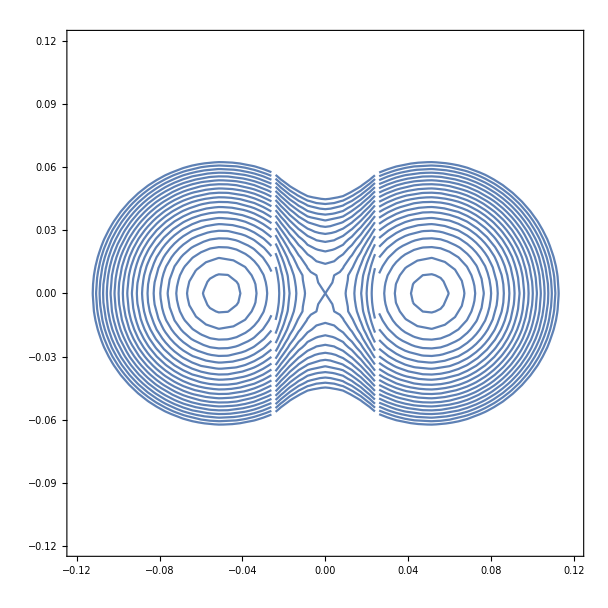

```mathematica
Table[ContourPlot[y^2/2+V2[x]== En,{x,-.12,.12},{y,- .12,.12}],{En,-0.001,0.001,0.0001}];
Show[%]
```

```mathematica
α = 0.2;
χ = a2;
x3 =α/2
x4=χ/2;
δ=-x4^2+β+x4 χ-1/2 χ^2;
β = x3^2-x3 α+ 1/2 α^2
H[x_,y_]:= Piecewise[{{1/2 y^2+ 1/2(x+α)^2,x≤ -x3},{1/2 y^2 -1/2 x^2+β,-x3<x≤ 0},{V2[y] x/x4+1/2 y^2(1-x/x4)-1/2 x^2+β,0<x≤ x4},{  V2[y]+1/2(x-χ)2+δ,x>x4}},x]
```

0.1

0.01

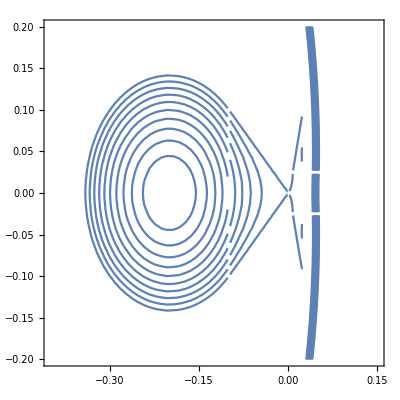

```mathematica
Table[ContourPlot[H[x,y]== En,{x,-0.4,0.15},{y,- 0.2,0.2}],{En,0,0.01,0.001}];
Show[%]
```

```mathematica
Manipulate[Plot[H[a,b],{a,-0.3,0.2}],{b,-2,2}]
```

```mathematica
ContourPlot[y^4+x^4+x^3+2 x^2 y^2-3 y^2 x== 0,
```

```mathematica
Manipulate[Module[{sol=NDSolve[{x'[t]==4 x[t]^2+3 x[t]^2-4 x[t] y[t]^2-3 y[t]^2,y'[t]==,y[0]== p[[2]],x[0]==p[[1]]},{x[t],y[t]},{t,0,T}]},ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,T},PlotRange->{{-4,2},{-2,2}}]],{{p,{2,1}},Locator},{{T,10},0,100}]
```

```mathematica
Clear[a,b,c,d,e,f,g]
```

```mathematica
F[x_,y_]:=(12b y^2+2 d x^2+2e x+6 g x y)(12a x^2+6c x+2 d y^2+6f x y)-(4 d x y + 2 e y+ 3 f x^2+3 g y^2)^2//Expand
```

```mathematica
F[x,y]
```

12 c e x^2+12 c d x^3+24 a e x^3+24 a d x^4-9 f^2 x^4+36 c g x^2 y-12 d f x^3 y+72 a g x^3 y-4 e^2 y^2+72 b c x y^2-12 d e x y^2+144 a b x^2 y^2-12 d^2 x^2 y^2+18 f g x^2 y^2-12 e g y^3+72 b f x y^3-12 d g x y^3+24 b d y^4-9 g^2 y^4

```mathematica
G[x_,y_]:=Evaluate[D[ D[F[x,y],{y,3}],{x,1}]]
G[0,0]/(2*3)//Simplify//Expand
```

72 b f-12 d g

```mathematica
a x^(4 +b x)
```

```mathematica
Solve[{24 a d - 9 f^2== 0,-9 g^2+24 b d== 0,-12d f + 72 a g== 0,144 a b - 12 d^2+18 f g== 0,72 b f - 12 d g==0},{a,b,d,f,g}]
```

{{a→(3 f^2)/(8 d),b→(2 d^3)/(27 f^2),g→(4 d^2)/(9 f)},{a→0,d→0,f→0,g→0},{b→0,d→0,f→0,g→0}}

```mathematica
test[x_,y_]:= (3 f^2)/(8 d)x^4+(2 d^3)/(27 f^2)y^4+d x^2 y^2+ f x^3 y +(4 d^2)/(9 f)x y^3
```

```mathematica
a=10;
f=-.1;
d=10;
Plot3D[test[x,y],{x,-a,a},{y,-a,a}]
```

-Graphics3D-

-1

1

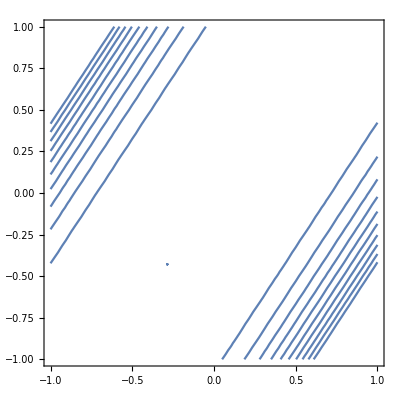

```mathematica
f=-1
d=1
Table[ContourPlot[test[x,y]== En,{x,-1,1},{y,- 1,1}],{En,-1,1,.1}];
Show[%]
```

```mathematica
H[x_,y_]:=a x^4+ b x^3 y + d x^2 y^2 +e x y^3 + f y^4 +
```

```mathematica
Plot3D[x^4+y^4,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
f[x,y]
```

4 x^3+x^4-4 x y^2+2 x^2 y^2+y^4

```mathematica
f[x,0]
```

4 x^3+x^4

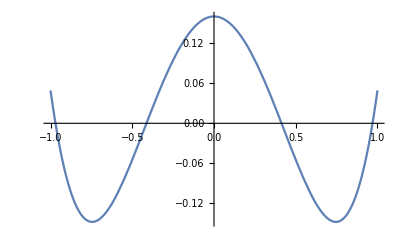

```mathematica
Plot[f[1/3,x],{x,-1,1}]
```

```mathematica
(24x+12 x^2)(12 y^2-2)//Expand//Factor
```

24 x (2+x) (-1+6 y^2)